```mathematica
f[x_]:=(4275)*((Sin[Pi*0.1*Sin[(x-4)/500]/(0.000546)]*(0.000546/(Pi*0.1*Sin[(x-4)/500])))^2)*(Cos[Pi*0.406*Sin[(x-4)/500]/0.000546]^2);
Table[f[x],{x,0,8,0.05}]
Needs["ErrorBarPlots`"].
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

{194.221,171.418,132.001,85.1141,41.5896,11.1667,0.011872,9.22155,34.7145,68.5208,101.072,123.816,131.397,122.811,101.24,72.7253,44.1296,21.0934,6.60113,0.568564,0.487741,2.804,4.46355,4.03775,2.01742,0.208297,0.526805,3.75433,8.85431,13.2579,14.1378,10.2488,3.58476,0.0273462,8.4076,37.9218,94.4886,177.184,276.132,373.007,444.661,469.387,434.358,342.065,213.486,86.2706,7.50807,22.1908,159.997,423.961,784.623,1182.21,1537.52,1769.75,1817.4,1656.99,1314.23,863.756,416.21,94.489,4.36435,206.397,696.525,1401.05,2188.52,2896.86,3370.12,3496.25,3236.69,2639.94,1834.8,1003.94,343.335,16.7908,116.433,638.88,1483.34,2472.66,3392.76,4041.46,Indeterminate,4041.46,3392.76,2472.66,1483.34,638.88,116.433,16.7908,343.335,1003.94,1834.8,2639.94,3236.69,3496.25,3370.12,2896.86,2188.52,1401.05,696.525,206.397,4.36435,94.489,416.21,863.756,1314.23,1656.99,1817.4,1769.75,1537.52,1182.21,784.623,423.961,159.997,22.1908,7.50807,86.2706,213.486,342.065,434.358,469.387,444.661,373.007,276.132,177.184,94.4886,37.9218,8.4076,0.0273462,3.58476,10.2488,14.1378,13.2579,8.85431,3.75433,0.526805,0.208297,2.01742,4.03775,4.46355,2.804,0.487741,0.568564,6.60113,21.0934,44.1296,72.7253,101.24,122.811,131.397,123.816,101.072,68.5208,34.7145,9.22155,0.011872,11.1667,41.5896,85.1141,132.001,171.418,194.221}

Data file Importing:

```mathematica
AppendTo[$Path,"Desktop/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"Users/emulder/GitHub/PhotonInterferenceLab/Analysis"];
AppendTo[$Path,"Users/ilipart/GitHub/PhotonInterferenceLab/Analysis"];
data2Slit = Import["4.45mmAll.csv"];
dataFarSlit = Import["4mmAll.csv"];
dataNearSlit = Import["5.9mmAll.csv"];
data2SlitAvg = Import["4.45mmAvg.csv"];
dataFarSlitAvg = Import["4mmAvg.csv"];
dataNearSlitAvg = Import["5.9mmAvg.csv"];
data2SlitError = Import["4.45mmError.csv"];
dataFarSlitError = Import["4mmError.csv"];
dataNearSlitError = Import["5.9mmError.csv"];
```

Fraunhofer Model for double slit and single slit: fit comparison with data and parameter optimization

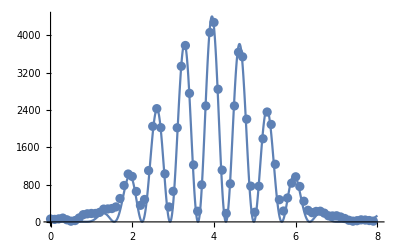

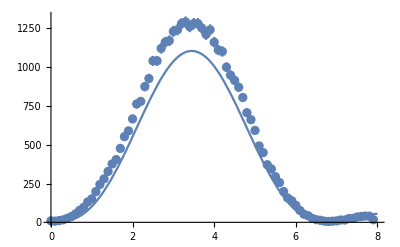

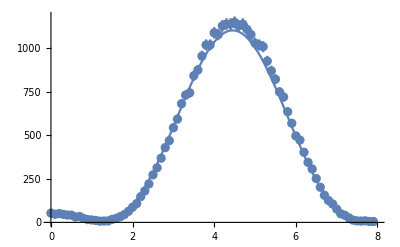

```mathematica
g[x_]:= I0*((Sin[Pi*a*Sin[(x-x0)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x0)/D2])))^2)*(Cos[Pi*d*Sin[(x-x0)/D2]/lambda]^2)+c;
I0 = 4400;
a = 0.085;
d = 0.406;
lambda = 0.000555;
x0 = 3.95;
c = 3.6;
D1=500;
D2=500;
fit = Plot[g[x],{x,0,8}];
dataPlot2Slit =ListPlot[data2Slit,PlotMarkers->{Automatic,8}];
dataPlot2SlitAvg=ErrorListPlot[Table[{data2SlitAvg[[i]],ErrorBar[.01,Flatten[data2SlitError][[i]]]},{i,80}]];
Show[fit,dataPlot2SlitAvg]

h[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x1)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x1)/D2])))^2)+c;
x1 = 3.45;
fit2 = Plot[h[x],{x,0,8},PlotRange->All];
dataPlotFarSlit = ListPlot[dataFarSlit,PlotMarkers->{Automatic,8}];
dataPlotFarSlitAvg=ErrorListPlot[Table[{dataFarSlitAvg[[i]],ErrorBar[.01,Flatten[dataFarSlitError][[i]]]},{i,80}]];
Show[fit2,dataPlotFarSlitAvg]

k[x_]:=I0*0.25*((Sin[Pi*a*Sin[(x-x2)/D2]/(lambda)]*(lambda/(Pi*a*Sin[(x-x2)/D2])))^2)+c;
x2 = 4.45;
fit3 = Plot[k[x],{x,0,8},PlotRange->All];
dataPlotNearSlit = ListPlot[dataNearSlit,PlotMarkers->{Automatic,8}];
dataPlotNearSlitAvg = ErrorListPlot[Table[{dataNearSlitAvg[[i]],ErrorBar[.01,Flatten[dataNearSlitError][[i]]]},{i,80}]];
Show[fit3,dataPlotNearSlitAvg]
```

Fresnel Model for double slit and single slit: fit comparison with data and parameter optimization

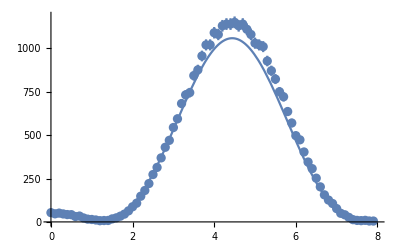

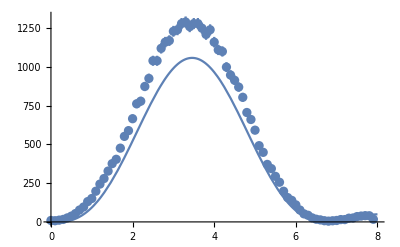

```mathematica
slit1[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0+(d/2),x0+(d/2)+a}]
s1[z_]:=33.3*I0*Re[slit1[z]*Conjugate[slit1[z]]]
slit2[z_]:=ⅇ^((2*π*I*D1)/lambda)*ⅇ^((2*π*I*D2)/lambda)*Integrate[ⅇ^((π*I*(x0-y)^2)/(D1*lambda))*ⅇ^((π*I*(y-z)^2)/(D2*lambda)),{y,x0-(d/2)-a,x0-(d/2)}]
s2[z_]:=33.3*I0*Re[slit2[z]*Conjugate[slit2[z]]]
fitb=Plot[s1[z],{z,0,8},PlotRange->All];
fitc=Plot[s2[z],{z,0,8},PlotRange->All];
Show[fitb,dataPlotNearSlitAvg]
Show[fitc,dataPlotFarSlitAvg]
```

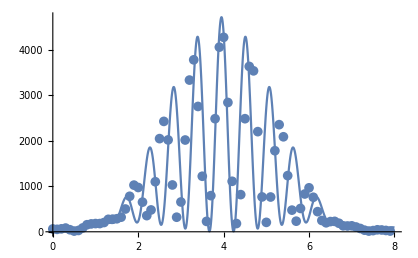

```mathematica
slitdouble[z_]:=slit1[z]+slit2[z]
slit[z_]:=40*I0*Re[slitdouble[z]*Conjugate[slitdouble[z]]]
fita=Plot[slit[z],{z,0,8}];
Show[fita,dataPlot2SlitAvg]
```

```mathematica
PearsonChiSquareTest[Table[data2SlitAvg[i],slit[i],{i,80}]]
```

Table::itform: Argument slit[i] at position 2 does not have the correct form for an iterator.

PearsonChiSquareTest::rctnln: The argument Table[data2SlitAvg[i], slit[i], {i, 80}] at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

PearsonChiSquareTest[Table[data2SlitAvg[i],slit[i],{i,80}]]

```mathematica
Table[{data2SlitAvg[[i]],slit[i]},{i,.01,8}]
```

Part::pkspec1: The expression 0.01 cannot be used as a part specification.

Part::pkspec1: The expression 1.01 cannot be used as a part specification.

Part::pkspec1: The expression 2.01 cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

{{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦0.01⟧,88.1128},{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦1.01⟧,113.45},{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦2.01⟧,254.799},{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦3.01⟧,923.142},{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦4.01⟧,4208.45},{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦5.01⟧,2857.14},{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦6.01⟧,366.776},{{{0,62.3333},{0.1,53.6667},{0.2,64.3333},{0.3,81.6667},{0.4,45},{0.5,15.3333},{0.6,29},{0.7,84.3333},{0.8,154.667},{0.9,173.333},{1,180.667},{1.1,180.667},{1.2,204},{1.3,274},{1.4,277.667},{1.5,286.333},{1.6,321.333},{1.7,500.667},{1.8,780.333},{1.9,1026},{2,973.667},{2.1,652},{2.2,355.333},{2.3,480},{2.4,1100.33},{2.5,2048.33},{2.6,2427.33},{2.7,2020},{2.8,1029.33},{2.9,320.333},{3,655.333},{3.1,2017.67},{3.2,3335.67},{3.3,3781},{3.4,2755.67},{3.5,1221},{3.6,228.333},{3.7,794.667},{3.8,2486.33},{3.9,4060},{4,4275.33},{4.1,2843.33},{4.2,1110},{4.3,181},{4.4,817},{4.5,2486.33},{4.6,3635.67},{4.7,3538.33},{4.8,2202},{4.9,766.333},{5,207},{5.1,764.333},{5.2,1782.33},{5.3,2355.33},{5.4,2088.67},{5.5,1235},{5.6,476},{5.7,233},{5.8,513},{5.9,830.667},{6,966.667},{6.1,759},{6.2,443},{6.3,248.333},{6.4,197.667},{6.5,224.333},{6.6,229},{6.7,187.667},{6.8,130.667},{6.9,127.333},{7,131},{7.1,105.333},{7.2,72.6667},{7.3,35},{7.4,15.6667},{7.5,26},{7.6,43.6667},{7.7,39.6667},{7.8,29.3333},{7.9,16.3333},{8,3.33333}}⟦7.01⟧,135.287}}

```mathematica
slit[1]
```

114.497